```mathematica
(* This notebook contains examples for the PET-function
-ActivityHP-          calculate the activity of a phase component (THERMOCALC activities)
*)
(* This top-cell must be run once before any example can be performed.  *)

(* Define the directory,where the PET-files reside (e.g. C:\Eigene Dateien\Pet) and load PET. *)$PetDirectory="C:\Dokumente und Einstellungen\dachsedgar\Eigene Dateien\Pet\Pet7.0";

SetDirectory[$PetDirectory];
DeclarePackage["DEFDAT`",{"Dataset"}];
Dataset[Dataset->HP32]; 

CalcFormula["hs78b"]; (* calculate mineral formulae for "hs78b", and site-fractions compatible with HP data set  *)
```

Message from -CalcFormula-: creating file "hs78b.fu".

```mathematica
(* _______________________________________________________________________________________
				Examples for use of the Pet-Function:		-ActivityHP-
_______________________________________________________________________________________ *)
(* Example 1: 
use the PET-function -ActivityHP- to calculate a symbolic expression for the ideal activity of a phase-component;
Values of p, t and x are irrelevant in this case   *)

ActivityHP[p,t,ann,"",ActivityMode->IdealActivitySymbolic]
```

aid(ann)=4.*XAlT1*XFeM1*XFeM2^2*XKA*XSiT1

```mathematica
(* Example 2a: 
use the PET-function -ActivityHP- to calculate the activity (real and ideal) of a phase-component (in this case for almandine from the garnet data in "hs78b"); 
The value of x is irrelevant in this case (also the values of P and T for a(id)). Note that you must have used CalcFormula["hs78b"] before and Dataset[Dataset->HP32]. *)

ActivityHP[5000,700,alm,x,ActivitySampleFile->"hs78b"]
```

{0.453088,a(alm)=GrtHP}

```mathematica
ActivityHP[5000,700,alm,x,ActivityMode->IdealActivity,ActivitySampleFile->"hs78b"]
```

{0.454987,a(alm)=Ideal}

```mathematica
(* Example 2b: use the PET-function-ActivityHP-to calculate the activity (real and ideal) of a order/disorder dependent phase-component:(in this case for annite from the biotite data in "hs78b"); 
Values of P and T are relevant in this case also for a(id), because for bt,site fractions are now temperature dependent according to the order/disorder model. The value of x is irrelevant. Note that you must have used CalcFormula["hs78b"] before and Dataset[Dataset->HP32]. *)

ActivityHP[5000,700,ann,x,ActivitySampleFile->"hs78b"]
ActivityHP[5000,700,ann,x,ActivityMode->IdealActivity,ActivitySampleFile->"hs78b"]
```

{0.0505124,a(ann)=BtHP}

{0.0535863,a(ann)=Ideal}

```mathematica
(* Example 3a: Explicit use of the <x> parameter for garnet: x = {x1,x2};
use the PET-function -ActivityHP- to calculate the activity of the almandine phase-component at P = 5000 bar, T = 500 C *)
(* For direct input, x in the call to -ActivityHP- must be a two-element list of the form:
x = {{x1=list of site fractions},{x2=list of end-member proportions}}; *)
(* Consulting the file ACTIVITYHPDAT.M shows that the activity model for garnet is: *)
(*  {{"grt",{{"",{"Mg","Ca","Fe","Mn"}},{"",{"Al","Fe3"}}}}   *)
(* x1 is thus the list: x1 = {{"Mg","Ca","Fe","Mn"}},{"Al","Fe3"}}, whereas
x2 = {"XPy","XGr","XAlm","XSp","XAndr"} 
(both can be copied from "hs78b.fu"). The result is identical to Example 2a. *)

x1 = {{0.09338,0.02539,0.76913,0.11211},{1.,0.}}; 
x2 = {0.09338,0.02539,0.76913,0.11211,0.};
ActivityHP[5000,700,alm,{x1,x2}]
```

{0.453088,a(alm)=GrtHP}

```mathematica
(* Example 3b: Explicit use of the <x> parameter for biotite: x = {x1,x2};
use the PET-function -ActivityHP- to calculate the activity of the order/disorder dependent phase-component phlogopite at P = 5000 bar, T = 700 K. The result is identical to Example 2b. *)
(* x1 is the following list of site fractions and can be copied from "hs78b.fu" ("nd" appears for site fractions that are order/disorder dependent and calculated at run time):
	{{"XKA"}, {"XMgM1", "XFeM1", "XAlM1"}, {"XMgM2", "XFeM2"}, {"XSiT1", "XAlT1"}} *)
x1 =  {{0.93847}, {"nd",       "nd",     0.50358},    {  "nd",          "nd"},    {0.37243, 0.62757}};
(* x2 for biotite is the following list  (copied from "hs78b.fu") : 
 {"y=XAl(M1)", "x=Fe/(Fe+Mg)", "Fe3", "Ti"} *)
x2= {0.50358,             0.50624,                 0.,     0.08129};
ActivityHP[5000,700,ann,{x1,x2}]
```

{0.0505124,a(ann)=BtHP}

```mathematica
(* Example 3c:
use the PET-function -ActivityHP- to calculate the order/disorder dependent site-fractions of biotite:
x1 and x2 are identical as in Example 3b. *)
x1 =  {{0.93847}, {"nd","nd",0.50358},{  "nd", "nd"},{0.37243, 0.62757}};
x2= {0.50358,0.50624, 0.,0.08129};
ActivityHP[5000,700,ann,{x1,x2},ActivityMode->SiteFractions]
```

{{bt,{{A,{K}},{M1,{Mg,Fe,Al}},{M2,{Mg,Fe}},{T1,{Si,Al}}}},{{0.93847},{0.0262884,0.388842,0.50358},{0.603679,0.396321},{0.37243,0.62757}}}

```mathematica
(* Example 3d:
use the PET-function -ActivityHP- to calculate the order parameter q of biotite:
x1 and x2 are identical as in Example 3b. *)
x1 =  {{0.93847}, {"nd","nd",0.50358},{  "nd", "nd"},{0.37243, 0.62757}};
x2= {0.50358,0.50624, 0.,0.08129};
ActivityHP[5000,700,ann,{x1,x2},ActivityMode->Q]
```

{0.329758,q(ann)=BtHP}

```mathematica
(* Example 4: use the PET-function -ActivityHP- to display the activity model of a phase-component: (in this case for biotite); 
Values of p, t and x are irrelevant in this case *)

ActivityHP[p,t,phl,x,ActivityMode->DisplayActivityModel]
```

Activity-model for: bt. Number 22 in data file.

{{A,{K}},{M1,{Mg,Fe,Al}},{M2,{Mg,Fe}},{T1,{Si,Al}}}

Ideal activity for: aid(phl) = 4. XAlT1 XKA XMgM1 XMgM2^2 XSiT1

There are 4 end-members: {phl,ann,east,obi}

Symmetric formalism Margules parameters (kJ):

Data displayed as {phl,ann,east,obi} x {phl,ann,east,obi} square matrix.

(0 | 9 | 10 | 3
0 | 0 | -1 | 6
0 | 0 | 0 | 10
0 | 0 | 0 | 0)

delta-H of ordering reaction (kJ): -32.3

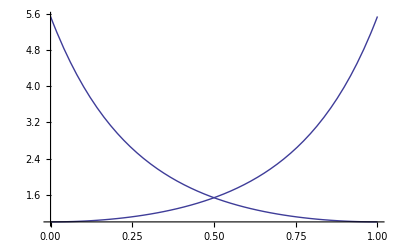

```mathematica
(* Example 5: use the PET-function -ActivityHP- to plot one-site normalized activity-coefficients of the pyrope- and grossular phase-components at P = 5000 bar, T = 500 C, along the grossular - pyrope join. *)
(* This examples does not specify a data file, but site fractions are directly used in the call to -ActivityHP- instead, similar as in Example 3a: *)
(* x1 = {{"Mg","Ca","Fe","Mn"}},{"Al","Fe3"}}
x2 = {"XPy","XGr","XAlm","XSp","XAndr"}  *)

plot1=Plot[ActivityHP[5000,773,py,{ {{1-x,x,0,0},{1,0}},{1-x,x,0,0,0}},ActivityMode->ActivityCoefficient][[1]]^(1/3),{x,0,1},PlotRange->All];
plot2=Plot[ActivityHP[5000,773,gr,{ {{1-x,x,0,0},{1,0}},{1-x,x,0,0,0}},ActivityMode->ActivityCoefficient][[1]]^(1/3),{x,0,1},PlotRange->All];
Show[plot1,plot2]
```

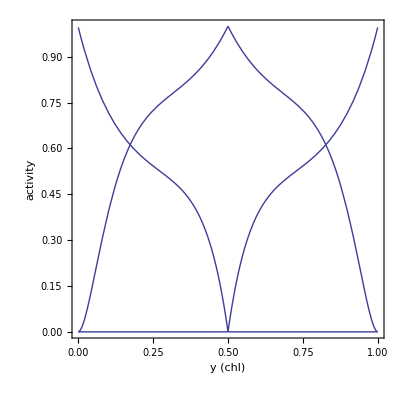

```mathematica
(* Example 6: calculate chlorite activities: this reproduces Fig. (4a) of Holland & Powell (1998);  
x1= {{"XMgM23","XFeM23"},{"XMgM1","XAlM1","XFeM1"},{"XMgM4","XAlM4"},{"XOH"},{"XSiT2","XAlT2"}},
x2 = {"y=XAl(T2)","x=Fe/Fe+Mg)"} *)

x1={{"nd","nd"},{"nd","nd","nd"},{"nd","nd"},{1.},{0.25295,0.74705}};
p1=Plot[ActivityHP[5000,550+273,clin,{x1,{y,0}},ActivityMode->RealActivity][[1]],{y,0.001,0.999}];
p2=Plot[ActivityHP[5000,550+273,ames,{x1,{y,0}},ActivityMode->RealActivity][[1]],{y,0.001,0.999}];
p3=Plot[ActivityHP[5000,550+273,afchl,{x1,{y,0}},ActivityMode->RealActivity][[1]],{y,0.001,0.999}];
Show[p1,p2,p3,PlotRange->{{0,1},{0,1}},Frame->True,FrameLabel->{"y (chl)","activity"},AspectRatio->1]
```

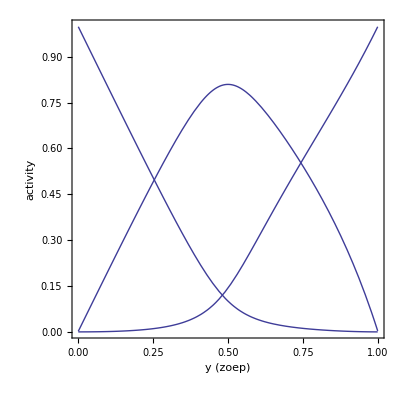

```mathematica
(* Example 7: calculate zoisite-epidote activities:  x1 = {{XCa},{XAlM1,XFe3M1},{XAlM3,XFe3M3}},
x2 = Fe3/(Fe3+Al(VI)-1} *)

x1={{1},{"nd","nd"},{"nd","nd"}};
p1=Plot[ActivityHP[5000,550+273,cz,{x1,{y}},ActivityMode->RealActivity][[1]],{y,0.001,0.999}];
p2=Plot[ActivityHP[5000,550+273,ep,{x1,{y}},ActivityMode->RealActivity][[1]],{y,0.001,0.999}];
p3=Plot[ActivityHP[5000,550+273,fep,{x1,{y}},ActivityMode->RealActivity][[1]],{y,0.001,0.999}];
Show[p1,p2,p3,PlotRange->{{0,1},{0,1}},Frame->True,FrameLabel->{"y (zoep)","activity"},AspectRatio->1]
```

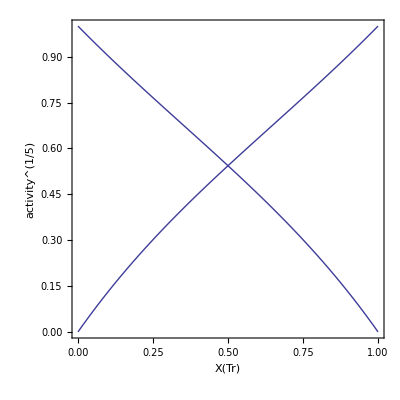

```mathematica
(* Example 8: plot amphibole activities; along the tremolite - tschermakite join;this reproduces the figure given on the homepage of T.J.B. Holland: http://www.esc.cam.ac.uk/astaff/holland/ds5/hornblendes/hb.html *)
(* As shown by the output of -CalcFormula-, x1 for amphibole is the list:
{{"XNaA","XKA","XVacA"},{"XCaM4","XNaM4"},{"XMgM13","XFeM13"},{"XMgM2","XFeM2","XAlM2","XFe3M2"},{"XSiT1","XAlT1"}};
whereas x2 is the list: {ptr,pfact,pts,pparg,pgl,pfts,pkpa} 
*)
p1a=Plot[ActivityHP[5000,550+273,tr,{{{0,0,1},{1,0},{xtr,1-xtr},{xtr,1-xtr,0,0},{1,0}},
{xtr,1-xtr,0,0,0,0,0}},ActivityMode->RealActivity][[1]]^(1/5),{xtr,0,1}];
p1b=Plot[ActivityHP[5000,550+273,fact,{{{0,0,1},{1,0},{xtr,1-xtr},{xtr,1-xtr,0,0},{1,0}},
{xtr,1-xtr,0,0,0,0,0}},ActivityMode->RealActivity][[1]]^(1/5),{xtr,0,1}];
Show[p1a,p1b,PlotRange->{{0,1},{0,1}},Frame->True,FrameLabel->{"X(Tr)","activity^(1/5)"},AspectRatio->1]
```

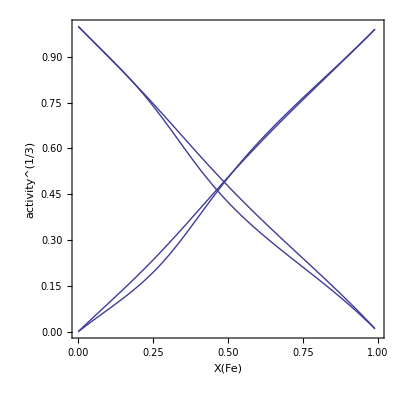

```mathematica
(* Example 9: activities along the annite - phlogopite join: this is a plot of Fig. 6 from Powell & Holland (1999): Am Min 84: 1-14;
As can be seen from the output of -CalcFormula-, 
x1 = {{XKA},{XMgM1,XFeM1,XAlM1},{XMgM2,XFeM2},{XSiT1,XAlT1}} and 
x2 = {XAl(M1), Fe/(Fe+Mg), Fe3+, Ti}  *)

p1=Plot[ActivityHP[1,500+273,phl,{{{1},{1-xfe,xfe,0},{1-xfe,xfe},{1/2,1/2}},{0,xfe,0,0}},
ActivityMode->RealActivity][[1]]^(1/3),{xfe,0.001,0.99}];
p2=Plot[ActivityHP[1,500+273,ann,{{{1},{1-xfe,xfe,0},{1-xfe,xfe},{1/2,1/2}}, {0,xfe,0,0}},
ActivityMode->RealActivity][[1]]^(1/3),{xfe,0.001,0.99}];
p3=Plot[ActivityHP[1,800+273,phl,{{{1},{1-xfe,xfe,0},{1-xfe,xfe},{1/2,1/2}}, {0,xfe,0,0}},
ActivityMode->RealActivity][[1]]^(1/3),{xfe,0.001,0.99}];
p4=Plot[ActivityHP[1,800+273,ann,{{{1},{1-xfe,xfe,0},{1-xfe,xfe},{1/2,1/2}}, {0,xfe,0,0}},
ActivityMode->RealActivity][[1]]^(1/3),{xfe,0.001,0.99}];
Show[p1,p2,p3,p4,PlotRange->{{0,1},{0,1}},Frame->True,FrameLabel->{"X(Fe)","activity^(1/3)"},AspectRatio->1]
```

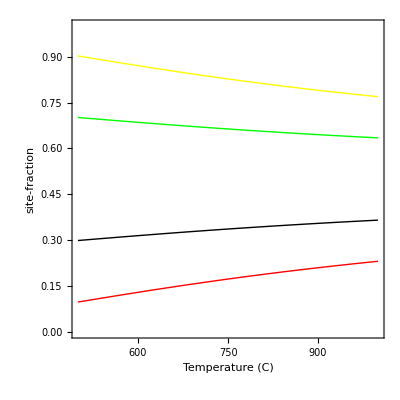

```mathematica
(* Example 10: plot order-dependent site-fractions of biotite for XFe = 0.5 as function of temperature:
x1 = {{XKA},{XMgM1,XFeM1,XAlM1},{XMgM2,XFeM2},{XSiT1,XAlT1}} and 
x2 = {XAl(M1), Fe/(Fe+Mg), Fe3+, Ti}  
black: XFe(M2), green: XMg(M2), red: XMg(M1), yellow: XFe(M1)
*)

xfe=0.5;
xmgm1=Plot[ActivityHP[1,t+273,ann,{{{1},{1-xfe,xfe,0},{1-xfe,xfe},{1/2,1/2}},{0,xfe,0,0}},
ActivityMode->SiteFractions][[2,2,1]],{t,500,1000},PlotStyle->RGBColor[1,0,0]];
xfem1=Plot[ActivityHP[1,t+273,ann,{{{1},{1-xfe,xfe,0},{1-xfe,xfe},{1/2,1/2}},{0,xfe,0,0}},
ActivityMode->SiteFractions][[2,2,2]],{t,500,1000},PlotStyle->RGBColor[1,1,0]];
xmgm2=Plot[ActivityHP[1,t+273,ann,{{{1},{1-xfe,xfe,0},{1-xfe,xfe},{1/2,1/2}},{0,xfe,0,0}},
ActivityMode->SiteFractions][[2,3,1]],{t,500,1000},PlotStyle->RGBColor[0,1,0]];
xfem2=Plot[ActivityHP[1,t+273,ann,{{{1},{1-xfe,xfe,0},{1-xfe,xfe},{1/2,1/2}},{0,xfe,0,0}},
ActivityMode->SiteFractions][[2,3,2]],{t,500,1000},PlotStyle->RGBColor[0,0,0]];
Show[xmgm1,xfem1,xmgm2,xfem2,PlotRange->{Automatic,{0,1}},Frame->True,FrameLabel->{"Temperature (C)","site-fraction"},AspectRatio->1]
```

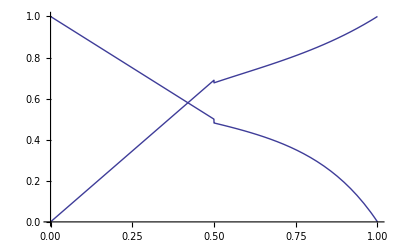

```mathematica
plot1=Plot[ActivityHP[1,973,ab,{ {{1-x,x}},{1-x,x}},ActivityMode->RealActivity][[1]],{x,0,1},PlotRange->All];
plot2=Plot[ActivityHP[1,973,an,{ {{1-x,x}},{1-x,x}},ActivityMode->RealActivity][[1]],{x,0,1},PlotRange->All];
Show[plot1,plot2]
```

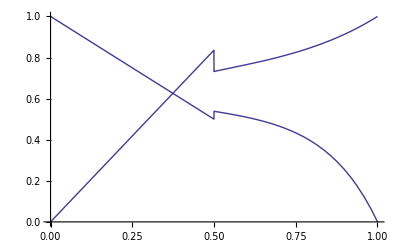

```mathematica
plot3=Plot[ActivityHP[1,773,ab,{ {{1-x,x}},{1-x,x}},ActivityMode->RealActivity][[1]],{x,0,1},PlotRange->All];
plot4=Plot[ActivityHP[1,773,an,{ {{1-x,x}},{1-x,x}},ActivityMode->RealActivity][[1]],{x,0,1},PlotRange->All];
Show[plot3,plot4]
```

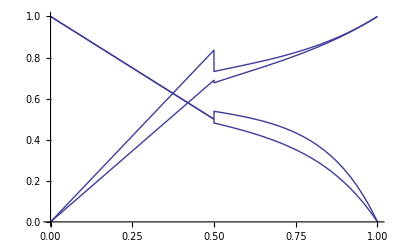

```mathematica
Show[plot1,plot2,plot3,plot4]
```